# k vs B Plot

## Based on 26 brussels eckhasu v3 p0

We plot k vs B  stable and unstable points.

## Definitions

### Calculations

GIVEN THE BRIUSELATOR DEPENDS ON (A,B,σ),
-FIND THE COEFFICIENTS OF GL’S ECUTIONS DEPENDING ON THESE PARAMETERS
-ESTABLISH THE CONDITIONS OF EXISTENCE WHEN THE COUPLING IS SMALL

```mathematica
(*Equilibrium point*)
X0=A;
Y0=B/A;
(*wave number at the bifucation*)
kc=(√A)/σ^(1/4);
(*the double bifurcation is reached when*)
BT=(1+A √σ)^2;
BH=1+A^2;
(*coefficients for the pure Turing mode*)
μt=Assuming[A>0,Simplify[B2/((1+A √σ)(1-σ)) /.{B2->B-BT}]];
at=Assuming[A>0,Simplify[(8-38 A √σ-5 A^2 σ+8 A^3 σ^(3/2))/(9 A^3 (-1+σ) √σ)]];
bt=Assuming[A>0,Simplify[(4 σ)/((1+A √σ) (1-σ))]];
```

Definimos las zonas:

```mathematica
(*the amplitude of the Turing mode (depends on B, A σ and R)*)
Z=(√(-bt R^2+μt))/(√at);
Z2=(-bt R^2+μt)(at);

plott1=RegionPlot[Evaluate[Z2 /.{A->1,σ->0.1}]>0,{R,-1.,1.0},{B,1.7,2},PlotStyle->Opacity[0.01,Red],BoundaryStyle->{Red}];

(*Eckhaus criterion*)
critEck=μt-3 bt R^2;
plott2=RegionPlot[Evaluate[critEck /.{A->1,σ->0.1}]>0,{R,-1.,1.0},{B,1.7,2},PlotStyle->Opacity[0.05,Orange],BoundaryStyle->{Orange,Dashed,Thickness[0.005]}];
plott4=Plot[2,{R,-0.81,.81},PlotStyle->{Opacity[1,Blue],Thickness[0.005]}];
plott3=Show[plott1,plott2,plott4];
```

```mathematica
plott1b=RegionPlot[Evaluate[Z2 /.{A->1,σ->0.1}]>0&&Evaluate[critEck /.{A->1,σ->0.1}]<0,{R,-1.,1.0},{B,1.7,2},PlotStyle->Opacity[0.05,Red],BoundaryStyle->{White},PlotPoints->120];
bexis=Solve[Evaluate[Z2 /.{A->1,σ->0.1}]==0,B][[1,1,2]];
plott1c=Plot[bexis,{R,-1.,1.0},PlotStyle->Opacity[1,Red],PlotRange->{1.72,2}];
plott2b=RegionPlot[Evaluate[critEck /.{A->1,σ->0.1}]>0,{R,-1.,1.0},{B,1.7,2},PlotStyle->Opacity[0.01,Orange],BoundaryStyle->{Orange,Dashed,Thickness[0.005]}];
plott4b=Plot[2,{R,-0.81,.81},PlotStyle->{Opacity[1,Blue],Thickness[0.006]}];
plott3b=Show[plott1b,plott1c,plott2b,plott4]; (*background*)
```

Values:

```mathematica
kc0=Evaluate[kc/.{A->1,σ->0.1}];
BT0=Evaluate[BT/.{A->1,σ->0.1}];
BH0=Evaluate[BH/.{A->1,σ->0.1}];
L=2 15 Pi/kc0;
f=2*Pi/L;
g=(BH0-BT0)/10;

tabla1=Table[{f*m,BT0+0.01+g*n},{m,-10,10,1},{n,0,10,1}];
```

```mathematica
turingBruselasestable2=Plot[0.22,{x,9,22},PlotRange->{{7,23},{0,0.4}},AspectRatio->0.75, Frame->True, FrameTicks->{{None,{0,0.14,0.22,0.31,0.39}},{None,{9,12,15,18,21}}}, ImageSize->500, FrameTicksStyle->Directive[Gray,28], FrameLabel->{Text[Style["n",38,Italic, Black]],Text[Style["ϵ",38,Italic, Black]]}];
```

```mathematica
nt={0,0.14,0.22,0.31,0.39};
```

```mathematica
(*to determine the value of k *)
kb=(√A)/σ^(1/4) ;(*bifurcation value k*)
Solve[kb^2==kb2,A]
```

{{A→kb2 √σ}}

```mathematica
kmin=(√(-1+B-A^2 σ))/(√2 √σ);(*minimum k of h*)
a1=Solve[kmin-kc==Δk1,B];
a11=Simplify[a1 /.{A->1,σ->0.1}][[1,1,2]];
tip1=Plot[a11,{Δk1,-0.9,0.9},PlotRange->{1.735,1.995},PlotStyle->{Purple,DotDashed,Thickness[0.0095]}];
```

```mathematica
kmax=√((-(-1+A^2+B) σ+(-1+A^2+B) σ^2+√(A^2 B σ (-1+σ^2)^2))/((-1+σ)^2 σ));
```

```mathematica
FullSimplify[kmax^2]
```

((-1+A^2+B) (-1+σ) σ+√(A^2 B σ (-1+σ^2)^2))/((-1+σ)^2 σ)

```mathematica
b1=Evaluate[Solve[kmax-kc==Δk2,B]/.{A->1,σ->0.1}][[1,1,2]];

tip2=Plot[b1,{Δk2,-0.9,0.9},PlotRange->{1.735,2},PlotStyle->{Purple,Dotted,Thickness[0.0095]}];
```

### Definitions:

```mathematica
U(*Unit*)=tabla1⟦12,2⟧-tabla1⟦11,1⟧;
a=1.742455532033676;
```

#### Stable Points:

```mathematica
Stable={{0.,1.82272},{0.,1.84947},{0.,1.74246},{0.,1.79596},{-0.118552,1.76921},{-0.118552,1.79596},{-0.237104,1.79596},{0.,1.76921},{0.118552,1.76921},{0.118552,1.79596},{-0.118552,1.82272},{-0.237104,1.82272},{-0.355656,1.82272},{0.118552,1.82272},{0.237104,1.82272},{-0.118552,1.84947},{-0.237104,1.84947},{-0.355656,1.84947},{0.118552,1.84947},{0.237104,1.84947},{0.,1.90298},{-0.237104,1.90298},{-0.355656,1.90298},{-0.118552,1.90298},{0.237104,1.90298},{0.118552,1.90298},{0.,1.87623},{0.237104,1.87623},{-0.237104,1.87623},{-0.355656,1.87623},{0.118552,1.87623},{-0.118552,1.87623},{0.,1.92974},{0.,1.95649},{0.,1.98325},{0.118552,1.95649},{-0.118552,1.95649},{-0.237104,1.95649},{-0.355656,1.95649},{-0.474208,1.95649},{0.118552,1.92974},{0.237104,1.92974},{-0.118552,1.92974},{-0.237104,1.92974},{-0.355656,1.92974},{-0.474208,1.92974},{-0.118552,1.98325},{-0.237104,1.98325},{-0.355656,1.98325},{-0.474208,1.98325},{0.118552,1.98325}};
```

```mathematica
lista1=ListPlot[Stable,PlotStyle->Directive[PointSize[0.02],Opacity[.5],Orange]];
```

```mathematica
(*First stable point*)
```

```mathematica
Stable2={{0.,1.82272},{0.,1.84947},{0.,1.74246},{0.,1.79596},{-0.118552,1.76921},{-0.118552,1.79596},{0.118552,1.76921},{-0.118552,1.82272},{-0.118552,1.84947},{-0.237104,1.84947},{-0.237104,1.90298},{-0.355656,1.90298},{-0.118552,1.90298},{-0.237104,1.87623},{-0.118552,1.87623},{-0.237104,1.95649},{-0.355656,1.95649},{-0.118552,1.92974},{-0.237104,1.92974},{-0.355656,1.92974},{-0.118552,1.98325},{-0.237104,1.98325},{-0.355656,1.98325},{0.118552,1.98325}};
lista1a=ListPlot[Stable2,PlotStyle->Directive[PointSize[0.02],Opacity[.5],Orange]];
```

#### Oscillating Points

```mathematica
oscilaEst={{0.237104,1.95649},{0.237104,1.98325}};
lista2=ListPlot[oscilaEst,PlotStyle->Directive[PointSize[0.02],Magenta]];
```

```mathematica
(*First oscillating point*)
oscilaEst2={{0.237104,1.95649}};
lista2a=ListPlot[oscilaEst2,PlotStyle->Directive[PointSize[0.02],Magenta]];
```

#### Unstable Points

```mathematica
unstableP={{-0.118552,1.74246},{-0.237104,1.76921}};
unstablePP={{-0.355656,1.79596},{-0.474208,1.84947},{-0.474208,1.90298},{-0.474208,1.87623},{-0.59276,1.95649},{-0.59276,1.98325}};
unstablePPP={{-0.474208,1.79596}};
unstablePPPP={{-0.474208,1.82272},{-0.59276,1.90298},{-0.711312,1.95649},{-0.59276,1.92974}};
unstablePPPPPPPP={{-0.829864,1.98325}};
unstablePPPPPPPPP={{-0.829864,1.95649}};
borrosa={{-0.237104,1.74246},{-0.355656,1.74246},{0.237104,1.74246},{0.355656,1.74246},{-0.474208,1.76921},{-0.355656,1.76921},{0.355656,1.76921},{-0.59276,1.79596},{-0.59276,1.82272},{0.474208,1.79596},{0.59276,1.82272},{0.59276,1.84947},{-0.59276,1.84947},{0.711312,1.90298},{-0.711312,1.90298},{-0.711312,1.87623},{0.711312,1.87623},{0.711312,1.92974},{-0.711312,1.92974}};
unstableM={{0.118552,1.74246},{0.237104,1.76921}};
unstableMM={{0.237104,1.79596}};
unstableMMM={{0.355656,1.79596},{0.355656,1.84947},{0.355656,1.87623}};
unstableMMMM={{0.355656,1.82272},{0.474208,1.82272}};
unstableMMMMM={{0.474208,1.84947},{0.474208,1.87623},{0.59276,1.87623},{-0.59276,1.87623},{0.474208,1.95649},{-0.711312,1.98325}};
unstableMMMMMM={{0.355656,1.90298},{0.474208,1.90298},{0.355656,1.95649},{0.355656,1.92974},{0.474208,1.92974},{0.59276,1.92974},{0.355656,1.98325},{0.474208,1.98325}};
unstableMMMMMMM={{0.59276,1.90298}};
unstableMMMMMMMM={{0.59276,1.95649},{0.59276,1.98325}};
unstableMMMMMMMMM={{0.711312,1.95649},{0.711312,1.98325}};
```

```mathematica
listainestable=Join[unstableP,unstablePP,unstablePPP,unstablePPPP,unstablePPPPPPPP,unstablePPPPPPPPP,unstableM,unstableMM,unstableMMM,unstableMMMM,unstableMMMMM,unstableMMMMMM,unstableMMMMMMM,unstableMMMMMMMM,unstableMMMMMMMMM];
lista3=ListPlot[listainestable,PlotStyle->Directive[PointSize[0.02],Opacity[0.4],Red]];
```

### Arrows

#### Functions to generate arrows

```mathematica
flechasizq(*left arrows*)[num_,alt_,inicio_]:=Module[{lista,kind=Thickness[0.003],kind2=Gray},lista={Graphics[{Arrowheads[{-0.02,-.001}],kind,kind2,Arrow[BezierCurve[{{0+inicio*U⟦1⟧,a+ (alt*U⟦2⟧)},{.5*U⟦1⟧+inicio*U⟦1⟧,a+ ((alt-1)*U⟦2⟧)+(0.85*U⟦2⟧)},{1*U⟦1⟧+inicio*U⟦1⟧,a+ (alt*U⟦2⟧)}}]]}],Graphics[{Arrowheads[{-0.02,-.001}],kind,kind2,Arrow[BezierCurve[{{0+inicio*U⟦1⟧,a+ (alt*U⟦2⟧)},{1*U⟦1⟧+inicio*U⟦1⟧,a+ ((alt-1)*U⟦2⟧)+(0.72*U⟦2⟧)},{2*U⟦1⟧+inicio*U⟦1⟧,a+ (alt*U⟦2⟧)}}]]}],Graphics[{Arrowheads[{-0.02,-.001}],kind,kind2,Arrow[BezierCurve[{{0+inicio*U⟦1⟧,a+ (alt*U⟦2⟧)},{1.5*U⟦1⟧+inicio*U⟦1⟧,a+ ((alt-1)*U⟦2⟧)+(0.61*U⟦2⟧)},{3*U⟦1⟧+inicio*U⟦1⟧,a+ (alt*U⟦2⟧)}}]]}],Graphics[{Arrowheads[{-0.02,-.001}],kind,kind2,Arrow[BezierCurve[{{0+inicio*U⟦1⟧,a+ (alt*U⟦2⟧)},{2*U⟦1⟧+inicio*U⟦1⟧,a+ ((alt-1)*U⟦2⟧)+(.5*U⟦2⟧)},{4*U⟦1⟧+inicio*U⟦1⟧,a+ (alt*U⟦2⟧)}}]]}],Graphics[{Arrowheads[{-0.02,-.001}],kind,kind2,Arrow[BezierCurve[{{0+inicio*U⟦1⟧,a+ (alt*U⟦2⟧)},{2.5*U⟦1⟧+inicio*U⟦1⟧,a+ ((alt-1)*U⟦2⟧)+(0.4*U⟦2⟧)},{5*U⟦1⟧+inicio*U⟦1⟧,a+ (alt*U⟦2⟧)}}]]}],Graphics[{Arrowheads[{-0.02,-.001}],kind,kind2,Arrow[BezierCurve[{{0+inicio*U[[1]],a+ (alt*U⟦2⟧)},{3*U⟦1⟧+inicio*U⟦1⟧,a+ ((alt-1)*U⟦2⟧)+ (0.3*U⟦2⟧)},{6*U⟦1⟧+inicio*U⟦1⟧,a+ (alt*U⟦2⟧)}}]]}],Graphics[{Arrowheads[{-0.02,-.001}],kind,kind2,Arrow[BezierCurve[{{0+inicio*U⟦1⟧,a+ (alt*U⟦2⟧)},{3.5*U⟦1⟧+inicio*U⟦1⟧,a+ ((alt-1)*U⟦2⟧)+(.2*U⟦2⟧)},{7*U⟦1⟧+inicio*U⟦1⟧,a+ (alt*U⟦2⟧)}}]]}],Graphics[{Arrowheads[{-0.02,-.001}],kind,kind2,Arrow[BezierCurve[{{0+inicio*U⟦1⟧,a+ (alt*U⟦2⟧)},{4*U⟦1⟧+inicio*U⟦1⟧,a+ ((alt-1)*U⟦2⟧)+(.1*U⟦2⟧)},{8*U⟦1⟧+inicio*U⟦1⟧,a+ (alt*U⟦2⟧)}}]]}],Graphics[{Arrowheads[{-0.02,-.001}],kind,kind2,Arrow[BezierCurve[{{0+inicio*U⟦1⟧,a+ (alt*U⟦2⟧)},{4.5*U⟦1⟧+inicio*U⟦1⟧,a+ ((alt-1)*U⟦2⟧)+(.0*U⟦2⟧)},{9*U⟦1⟧+inicio*U⟦1⟧,a+ (alt*U⟦2⟧)}}]]}]};Show[lista[[num⟦1⟧;;num⟦2⟧]]]]
```

```mathematica
flechasderec(*right arrows*)[num_,alt_,inicio_]:=Module[{lista,kind=Gray,kind2=Thickness[0.003]},lista={Graphics[{Arrowheads[{.001,0.02}],kind,kind2,Arrow[BezierCurve[{{(-1+inicio)*U⟦1⟧,a+ (alt*U⟦2⟧)},{-.5*U⟦1⟧+inicio*U⟦1⟧,a+ ((alt-1)*U⟦2⟧)+(0.85*U⟦2⟧)},{0+inicio*U⟦1⟧,a+ (alt*U⟦2⟧)}}]]}],Graphics[{Arrowheads[{.001,0.02}],kind,kind2,Arrow[BezierCurve[{{(-2+inicio)*U⟦1⟧,a+ (alt*U⟦2⟧)},{-1*U⟦1⟧+inicio*U⟦1⟧,a+ ((alt-1)*U⟦2⟧)+(0.72*U⟦2⟧)},{0+inicio*U⟦1⟧,a+ (alt*U⟦2⟧)}}]]}],Graphics[{Arrowheads[{.001,0.02}],kind,kind2,Arrow[BezierCurve[{{(-3+inicio)*U⟦1⟧,a+ (alt*U⟦2⟧)},{-1.5*U⟦1⟧+inicio*U⟦1⟧,a+ ((alt-1)*U⟦2⟧)+(0.61*U⟦2⟧)},{0+inicio*U⟦1⟧,a+ (alt*U⟦2⟧)}}]]}],Graphics[{Arrowheads[{.001,0.02}],kind,kind2,Arrow[BezierCurve[{{(-4+inicio)*U⟦1⟧,a+ (alt*U⟦2⟧)},{-2*U⟦1⟧+inicio*U⟦1⟧,a+ ((alt-1)*U⟦2⟧)+(.5*U⟦2⟧)},{0+inicio*U⟦1⟧,a+ (alt*U⟦2⟧)}}]]}],Graphics[{Arrowheads[{.001,0.02}],kind,kind2,Arrow[BezierCurve[{{(-5+inicio)*U⟦1⟧,a+ (alt*U⟦2⟧)},{-2.5*U⟦1⟧+inicio*U⟦1⟧,a+ ((alt-1)*U⟦2⟧)+(0.4*U⟦2⟧)},{0+inicio*U⟦1⟧,a+ (alt*U⟦2⟧)}}]]}],Graphics[{Arrowheads[{.001,0.02}],kind,kind2,Arrow[BezierCurve[{{(-6+inicio)*U⟦1⟧,a+ (alt*U⟦2⟧)},{-3*U⟦1⟧+inicio*U⟦1⟧,a+ ((alt-1)*U⟦2⟧)+ (0.3*U⟦2⟧)},{0+inicio*U⟦1⟧,a+ (alt*U⟦2⟧)}}]]}],Graphics[{Arrowheads[{.001,0.02}],kind,kind2,Arrow[BezierCurve[{{(-7+inicio)*U⟦1⟧,a+ (alt*U⟦2⟧)},{-3.5*U⟦1⟧+inicio*U⟦1⟧,a+ ((alt-1)*U⟦2⟧)+(.2*U⟦2⟧)},{0+inicio*U⟦1⟧,a+ (alt*U⟦2⟧)}}]]}],Graphics[{Arrowheads[{.001,0.02}],kind,kind2,Arrow[BezierCurve[{{(-8+inicio)*U⟦1⟧,a+ (alt*U⟦2⟧)},{-4*U⟦1⟧+inicio*U⟦1⟧,a+ ((alt-1)*U⟦2⟧)+(.1*U⟦2⟧)},{0+inicio*U⟦1⟧,a+ (alt*U⟦2⟧)}}]]}],Graphics[{Arrowheads[{.001,0.02}],kind,kind2,Arrow[BezierCurve[{{(-9+inicio)*U⟦1⟧,a+ (alt*U⟦2⟧)},{-4.5*U⟦1⟧+inicio*U⟦1⟧,a+ ((alt-1)*U⟦2⟧)+(0*U⟦2⟧)},{0+inicio*U⟦1⟧,a+ (alt*U⟦2⟧)}}]]}]};Show[lista⟦num⟦1⟧;;num⟦2⟧⟧]]
```

#### We define the arrows:

```mathematica
flechasiz={flechasizq[{6,6},9,-3],flechasizq[{6,6},9,-2],flechasizq[{5,6},8,-2],flechasizq[{6,6},7,-1],flechasizq[{6,6},7,-2],flechasizq[{6,6},7,-3],flechasizq[{6,7},6,-2],flechasizq[{6,6},6,-3],flechasizq[{5,5},5,0],flechasizq[{5,5},5,-1],flechasizq[{3,3},5,0],flechasizq[{5,5},4,-1],flechasizq[{3,3},4,0],flechasizq[{4,4},3,-1],flechasizq[{4,4},3,0],flechasizq[{2,3},2,0],flechasizq[{1,1},1,1],flechasizq[{1,1},0,0],flechasizq[{8,9},9,-3],flechasizq[{8,9},8,-3]};
```

```mathematica
flechasde={flechasderec[{2,2},9,-3],flechasderec[{5,5},9,-1],flechasderec[{2,2},8,-3],flechasderec[{4,4},8,-2],flechasderec[{4,4},7,-1],flechasderec[{2,2},6,-2],flechasderec[{4,4},6,-1],flechasderec[{2,2},5,-2],flechasderec[{5,5},5,0],flechasderec[{2,2},4,-2],flechasderec[{4,4},3,0],flechasderec[{2,3},2,-1],flechasderec[{1,1},1,-1],flechasderec[{1,1},0,0],flechasderec[{8,8},9,1],flechasderec[{9,9},8,2]};
```

## Stable

We plot stable (list1) and oscillating (list5) points, along with the borders (plott3).

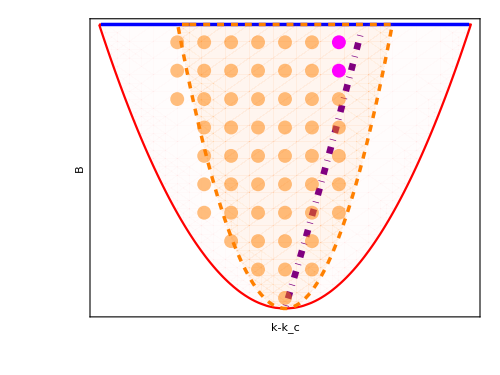

```mathematica
turingBruselasestable=Show[plott3,tip1,lista1,lista2,PlotRange->{{-0.825,0.825},{1.73,2}},AspectRatio->0.75, Frame->True, FrameTicks->{{None,{1.732,1.769,1.822,1.903,2}},{None,{-0.3,-0.6,-0.9,0,0.3,0.6,0.9}}}, ImageSize->500, FrameTicksStyle->Directive[Gray,28], FrameLabel->{Text[Style["k-k_c",38,Italic, Black]],Text[Style["B",38,Italic, Black]]}]
```

We export the graph

```mathematica
Export["turBruselasestable.png",turingBruselasestable,ImageResolution->250]
```

turBruselasestable.png

## Unstable with arrows

We plot the unstable (list3) points, stable where an unstable one ends (list1a) and oscillating where an unstable one ends (list2a), along with the borders (plott3) and the left arrows (arrowsiz) and right arrows (arrowsde).

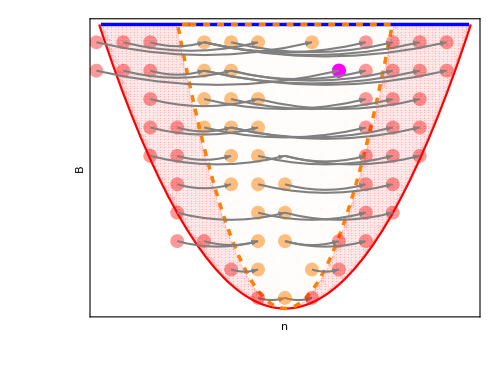

```mathematica
turingBruselasflechasv1=Show[plott3b,lista3,lista2a,lista1a,flechasiz,flechasde,PlotRange->{{-0.825,0.825},{1.73,2}},AspectRatio->0.75, FrameTicks->{{None,{1.732,1.769,1.822,1.903,2}},{None,{-0.3,-0.6,-0.9,0,0.3,0.6,0.9}}}, ImageSize->500, FrameTicksStyle->Directive[Gray,28], FrameLabel->{Text[Style["n",38,Italic, Black]],Text[Style["B",38,Italic, Black]]}]
```

Exportamos:

```mathematica
Export["turBruselasfelchasv1.png",turingBruselasflechasv1,ImageResolution->250]
```

turBruselasfelchasv1.png